```mathematica
(***************************БЛОК ВВОДА материальных параматеров**********************************************)
(*холестерик*)
{ϵ1 = 1,ϵ2 = 1.2,q =10, L =1};
(*траектория, заряд*)
{β3=1,Z =1,e=1};
```

```mathematica
(********************************БЛОК ИНИЦИАЛИЗАЦИИ******************************)
long ={k0= √ϵ2 ko,k3 =  √(ϵ2 ko^2-kp^2), δϵ =(ϵ1 - ϵ2)/ϵ2, kp=ko np ,n3= (√(ϵ2 ko^2-kp^2))/ko,Subscript[n, 3]= (√(ko^2-kp^2))/ko};
(*формула 150*)
w=(1+δϵ/2+δϵ^2 k0^2/(16 q^2))^(1/2);
{vp=((1+δϵ/2)k0^2 + 2q k0 w+q^2)^(1/2),vm =((1+δϵ/2)k0^2 - 2q k0 w+q^2)^(1/2) }; 
(*формула 149*)
{p01 = q+vp,p02 = q+vm};
{a0m1 = 2/(δϵ k0^2)(p01^2-k0^2(1+δϵ/2)), a0m2=2/(δϵ k0^2)(p02^2-k0^2(1+δϵ/2))};
(*формула 209*)
{Subscript[a, 1]=a0m1,Subscript[a, 2]=a0m2, Subscript[p, 1]=p01, Subscript[p, 2]=p02};
(*формула 210*)
dn = (Subscript[p, 1](Subscript[a, 1]-1)(Subscript[a, 2]+1)-Subscript[p, 2](Subscript[a, 1]+1)(Subscript[a, 2]-1)-2 Subscript[a, 1]+2 Subscript[a, 2])(Subscript[p, 1](Subscript[a, 1]+1)(Subscript[a, 2]-1)-Subscript[p, 2](Subscript[a, 1]-1)(Subscript[a, 2]+1)+2 Subscript[a, 1]-2 Subscript[a, 2]);
(*формула 211*)
ζp1 =(ko -Subscript[p, 2]+2q)(Subscript[p, 1]-Subscript[p, 2])Subscript[a, 1] Subscript[a, 2]^2-( ko+Subscript[p, 2])(Subscript[p, 1]+Subscript[p, 2]-2 q)Subscript[a, 1]+2(Subscript[p, 2]-q)( ko+Subscript[p, 1])Subscript[a, 2];
ζp2 =( ko -Subscript[p, 1]+2q)(Subscript[p, 2]-Subscript[p, 1])Subscript[a, 2] Subscript[a, 1]^2-( ko+Subscript[p, 1])(Subscript[p, 2]+Subscript[p, 1]-2 q)Subscript[a, 2]+2(Subscript[p, 1]-q)(ko+Subscript[p, 2])Subscript[a, 1];
σp1 = ( ko+Subscript[p, 2]+2q)(Subscript[p, 1]+Subscript[p, 2]-2q)Subscript[a, 2]^2-2(Subscript[p, 2]-q)( ko+Subscript[p, 1]-2q)Subscript[a, 1] Subscript[a, 2]-( ko-Subscript[p, 2])(Subscript[p, 1]-Subscript[p, 2]);
σp2 = ( ko+Subscript[p, 1]+2q)(Subscript[p, 2]+Subscript[p, 1]-2q)Subscript[a, 1]^2-2(Subscript[p, 1]-q)( ko+Subscript[p, 2]-2q)Subscript[a, 2] Subscript[a, 1]-(ko-Subscript[p, 1])(Subscript[p, 2]-Subscript[p, 1]);
ζm1 =(- ko -Subscript[p, 2]+2q)(Subscript[p, 1]-Subscript[p, 2])Subscript[a, 1] Subscript[a, 2]^2-(-ko+Subscript[p, 2])(Subscript[p, 1]+Subscript[p, 2]-2 q)Subscript[a, 1]+2(Subscript[p, 2]-q)(- ko+Subscript[p, 1])Subscript[a, 2];
ζm2 =(-ko -Subscript[p, 1]+2q)(Subscript[p, 2]-Subscript[p, 1])Subscript[a, 2] Subscript[a, 1]^2-(-ko+Subscript[p, 1])(Subscript[p, 2]+Subscript[p, 1]-2 q)Subscript[a, 2]+2(Subscript[p, 1]-q)(- ko+Subscript[p, 2])Subscript[a, 1];
σm1 = (- ko+Subscript[p, 2]+2q)(Subscript[p, 1]+Subscript[p, 2]-2q)Subscript[a, 2]^2-2(Subscript[p, 2]-q)(- ko+Subscript[p, 1]-2q)Subscript[a, 1] Subscript[a, 2]-(- ko-Subscript[p, 2])(Subscript[p, 1]-Subscript[p, 2]);
σm2 = (- ko+Subscript[p, 1]+2q)(Subscript[p, 2]+Subscript[p, 1]-2q)Subscript[a, 1]^2-2(Subscript[p, 1]-q)(- ko+Subscript[p, 2]-2q)Subscript[a, 2] Subscript[a, 1]-(- ko-Subscript[p, 1])(Subscript[p, 2]-Subscript[p, 1]);

(*коэффициеты определнные в 158*)
rr1 = √2 dn^-1 ζp1 KroneckerDelta[s,1]-√2 dn^-1 σp1 KroneckerDelta[s,-1];
rr2 = √2 dn^-1 ζp2 KroneckerDelta[s,1]-√2 dn^-1 σp2 KroneckerDelta[s,-1];
ll1 = -√2 dn^-1 σm1 KroneckerDelta[s,1] + √2 dn^-1 ζm1 KroneckerDelta[s,-1];
ll2 = -√2 dn^-1 σm2 KroneckerDelta[s,1] + √2 dn^-1 ζm2 KroneckerDelta[s,-1];
(*ветви дисперсии*)
p31 = p01 - kp^2/(2k0 w vp)((1+δϵ/4)(1+k0 w/q)+(δϵ^2 k0^2)/(16 q^2));
p32 = p02 +  kp^2/(2k0 w vm)((1+δϵ/4)(1-k0 w/q)+(δϵ^2 k0^2)/(16 q^2));
(*********************коэффициенты ряда фурье ************************)
(*формула 207*)
(*KroneckerDelta[n,\pm2] говорит что это,например ap1[p3\pm2q]*)
ap1[n_] :=((-kp^2 δϵ)/(64q) (q+vp+k0 w+(δϵ k0^2)/(4 q))/(q^2+q vp + k0 w(3q + vp)/2+(1+δϵ/2)k0^2/2))KroneckerDelta[n,2] +(-(5 kp^2)/(16 q^2) ((q-3vp/5+5k0 w/5)(q+vp + k0 w +(δϵ k0^2)/(4q)))/(q^2-q vp + k0 w(3q - vp)/2+(1+δϵ/2)k0^2/2))KroneckerDelta[n,-2];

am1[n_]:=(-(5 kp^2)/(16 q^2) ((q+3vp/5+5k0 w/5)(q+vp + k0 w +(δϵ k0^2)/(4q)))/(q^2+q vp + k0 w(3q + vp)/2+(1+δϵ/2)k0^2/2))KroneckerDelta[n,0]+( a0m1 + (2 kp^2 q^2)/(δϵ k0^4)(1+vp^-1+k0/(w vp)(1+δϵ/4(3+vp+(k0 w)/q)+(δϵ^2 k0^2)/(16 q^2))))KroneckerDelta[n,-2]+( (-kp^2 δϵ)/(64q) (q+vp+k0 w+(δϵ k0^2)/(4 q))/(q^2-q vp + k0 w(3q - vp)/2+(1+δϵ/2)k0^2/2))KroneckerDelta[n,-4];
(*формула 208*)

ap2[n_]:=((-kp^2 δϵ)/(64q) (q+vm-k0 w+(δϵ k0^2)/(4 q))/(q^2+q vm - k0 w(3q + vm)/2+(1+δϵ/2)k0^2/2))KroneckerDelta[n,2]+ ( -(5 kp^2)/(16 q^2) ((q-3vm/5-5k0 w/5)(q+vm - k0 w +(δϵ k0^2)/(4q)))/(q^2+q vm - k0 w(3q + vm)/2+(1+δϵ/2)k0^2/2))KroneckerDelta[n,-2];
am2[n_]:=(-(5 kp^2)/(16 q^2) ((q+3vm/5-5k0 w/5)(q+vm - k0 w +(δϵ k0^2)/(4q)))/(q^2+q vm - k0 w(3q + vm)/2+(1+δϵ/2)k0^2/2))KroneckerDelta[n,0]+( a0m2 + (2 kp^2 q^2)/(δϵ k0^4)(1+vm^-1-k0/(w vm)(1+δϵ/4(3-vm+(k0 w)/q)+(δϵ^2 k0^2)/(16 q^2))))KroneckerDelta[n,-2]+( (-kp^2 δϵ)/(64q) (q+vm-k0 w+(δϵ k0^2)/(4 q))/(q^2-q vm - k0 w(3q - vm)/2+(1+δϵ/2)k0^2/2))KroneckerDelta[n,-4];
(*******нормировочный множитель******************)
cSqrd = (ν0+2Re[(ν1 ⅇ^(ⅈ(p31+p32)L)+ν2 ⅇ^(-2ⅈ p31 L)+ν3 ⅇ^(-2ⅈ p32 L)+ν4 ⅇ^(ⅈ(p31-p32)L))])^-1;
ν0 = 1/(4 ko^2 dn^2)((((ko+Subscript[p, 1])^2+(ko+Subscript[p, 1]-2q)^2 Subscript[a, 1]^2)(ζp1)^2+((ko-Subscript[p, 1])^2+(ko-Subscript[p, 1]+2q)^2 Subscript[a, 1]^2)(σm1)^2)+(((ko+Subscript[p, 2])^2+(ko+Subscript[p, 2]-2q)^2 Subscript[a, 2]^2)(ζp2)^2+((ko-Subscript[p, 2])^2+(ko-Subscript[p, 2]+2q)^2 Subscript[a, 2]^2)(σm2)^2))KroneckerDelta[s,1] +1/(4 ko^2 dn^2)((((ko+Subscript[p, 1])^2+(ko+Subscript[p, 1]-2q)^2 Subscript[a, 1]^2)(σp1)^2+((ko-Subscript[p, 1])^2+(ko-Subscript[p, 1]+2q)^2 Subscript[a, 1]^2)(ζm1)^2)+(((ko+Subscript[p, 2])^2+(ko+Subscript[p, 2]-2q)^2 Subscript[a, 2]^2)(σp2)^2+((ko-Subscript[p, 2])^2+(ko-Subscript[p, 2]+2q)^2 Subscript[a, 2]^2)(ζm2)^2))KroneckerDelta[s,-1];
ν1 =-1/(4 ko^2 dn^2)(((ko-Subscript[p, 2])(ko+Subscript[p, 1]-2q)Subscript[a, 1]+(ko+Subscript[p, 1])(ko-Subscript[p, 2]+2q)Subscript[a, 2])ζp1 σm2 +((ko-Subscript[p, 1])(ko+Subscript[p, 2]-2q)Subscript[a, 2]+(ko+Subscript[p, 2])(ko-Subscript[p, 1]+2q)Subscript[a, 1])ζp2 σm1) KroneckerDelta[s,1]+-1/(4 ko^2 dn^2)(((ko-Subscript[p, 2])(ko+Subscript[p, 1]-2q)Subscript[a, 1]+(ko+Subscript[p, 1])(ko-Subscript[p, 2]+2q)Subscript[a, 2])σp1 ζm2 +((ko-Subscript[p, 1])(ko+Subscript[p, 2]-2q)Subscript[a, 2]+(ko+Subscript[p, 2])(ko-Subscript[p, 1]+2q)Subscript[a, 1])σp2 ζm1) KroneckerDelta[s,-1];
ν2 = (-Subscript[a, 1])/(2 ko^2 dn^2)(ko^2-Subscript[p, 1](Subscript[p, 1]-2q))ζp1 σm1 KroneckerDelta[s,1]+(-Subscript[a, 1])/(2 ko^2 dn^2)(ko^2-Subscript[p, 1](Subscript[p, 1]-2q))σp1 ζm1 KroneckerDelta[s,-1];
ν3 = (-Subscript[a, 2])/(2 ko^2 dn^2)(ko^2-Subscript[p, 2](Subscript[p, 2]-2q))ζp2 σm2 KroneckerDelta[s,1]+(-Subscript[a, 2])/(2 ko^2 dn^2)(ko^2-Subscript[p, 2](Subscript[p, 2]-2q))σp2 ζm2 KroneckerDelta[s,-1];
ν4 = 1/(4 ko^2 dn^2)(((ko+Subscript[p, 1])(ko+Subscript[p, 2])+(ko+Subscript[p, 1]-2q)(ko+Subscript[p, 2]-2q)Subscript[a, 1] Subscript[a, 2])ζp1 ζp2+((ko-Subscript[p, 1])(ko-Subscript[p, 2])+(ko-Subscript[p, 1]+2q)(ko-Subscript[p, 2]+2q)Subscript[a, 1] Subscript[a, 2])σm1 σm2)KroneckerDelta[s,1]+1/(4 ko^2 dn^2)(((ko+Subscript[p, 1])(ko+Subscript[p, 2])+(ko+Subscript[p, 1]-2q)(ko+Subscript[p, 2]-2q)Subscript[a, 1] Subscript[a, 2])σp1 σp2+((ko-Subscript[p, 1])(ko-Subscript[p, 2])+(ko-Subscript[p, 1]+2q)(ko-Subscript[p, 2]+2q)Subscript[a, 1] Subscript[a, 2])ζm1 ζm2)KroneckerDelta[s,-1];
(************гармоники*****************************************)
y1[n_] := ko-β3 (p31 + 2 q n);
y2[n_] := ko-β3 (p32 + 2 q n);
yy1[n_]:= ko+β3(p31 + 2 q n);
yy2[n_]:= ko+β3(p32 + 2 q n);
δN[x_]:= Sin[L/β3  x/2]/(π x);
(**************условия применимости*************************************************)
TheoryCheck[so_,mo_,koo_,npo_]:=Module[{},Qnum={s-> -1, m->-2,np->0.01,ko-> 5};
exp0 = kp^2/k0^2/.Qnum;
exp1 = kp^2/k0^2 q/Abs[k0-q]/.Qnum;
exp2 = kp^2/(Abs[k0-q]Abs[k0-2q])(δϵ^2 k0^2)/(256 q^2)/.Qnum;
check=(δϵ^2 k0^2)/(16 q^2)/.Qnum;
exp3 =(Abs[δϵ]k0)/(16q)kp^2/k0^2/.Qnum;
Print["Первая опция: ", check,"?<< 1"];
Print[exp0,"?<< 1; ",exp1, "?<< 1; ",exp2, "?<< 1;" ];
Print["Вторая опция", check,"?>> 1"];
Print[exp0,"?<< 1; ",exp3, "?<< 1; " ];
]
(***********************вероятность, vrch (169)****************************)
(*ВАЖНО! Сумма конечная*)
dP := Abs[Z e β3]cSqrd Sum[ (δN[y1[n]]^2 Abs[rr1]^2 KroneckerDelta[m,s+2n+1]+δN[yy1[n]]^2 Abs[ll1]^2 KroneckerDelta[m,s-2n-1])(p31+2q n)^2(ap1[2 n]+am1[2 n])^2+(δN[y2[n]]^2 Abs[rr2]^2 KroneckerDelta[m,s+2n+1]+δN[yy2[n]]^2 Abs[ll2]^2 KroneckerDelta[m,s-2n-1])(p32+2q n)^2(ap2[2 n]+am2[2 n])^2,{n,-20,20}] np^2/(8 ϵ2^2);
GetProbability[so_,mo_,koo_,npo_]:=Module[{},
dP/.{s-> so, m->mo,np->npo,ko-> koo}
]
```

Первая опция: 0.000520833?<< 1

0.0000833333?<< 1; 0.000184253?<< 1; 1.23898×10^-9?<< 1;

Вторая опация0.000520833?>> 1

0.0000833333?<< 1; 4.75454×10^-7?<< 1;

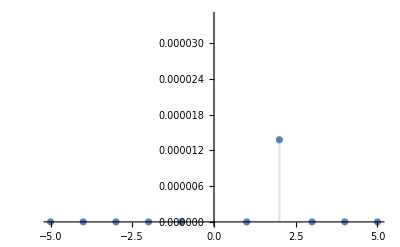

```mathematica
(**************БЛОК ВЫВОДА****************************)
TheoryCheck[1,2,5,0.1]
DiscretePlot[GetProbability[1,m,5,0.1]/.{s-> 1,np->0.1,ko-> 5},{m,-5,5}]
```

```mathematica
GetProbability[1,0,5,0.1]
GetProbability[1,2,5,0.1]
```

0.000354974

0.0000137896